DELTA = 0.02; Series: Zx = 1, 2, 2.2

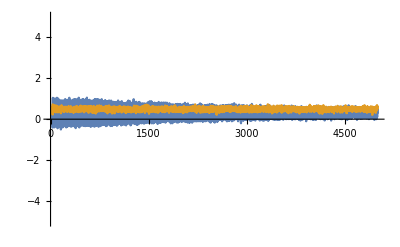

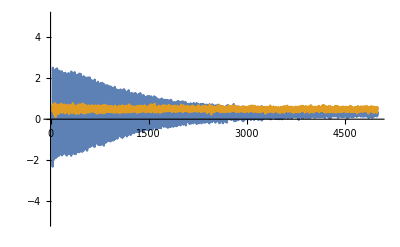

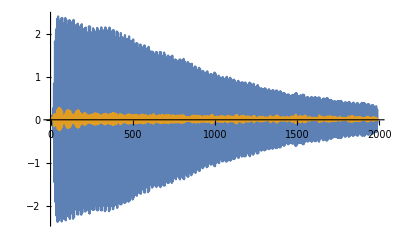

DELTA = 0; Series: Zx =

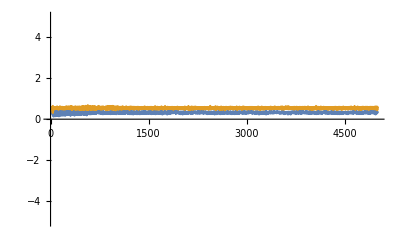

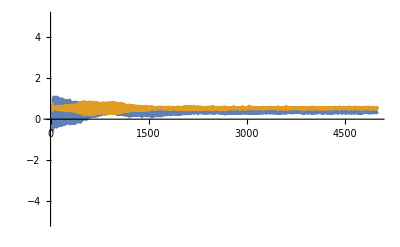

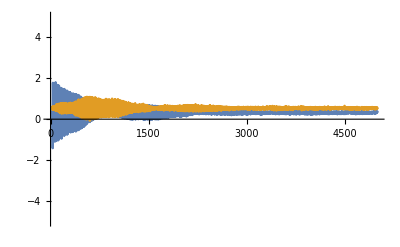

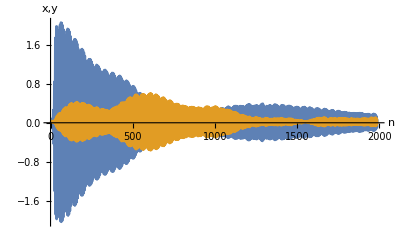

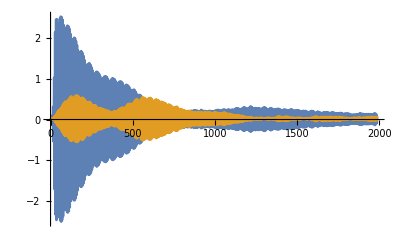

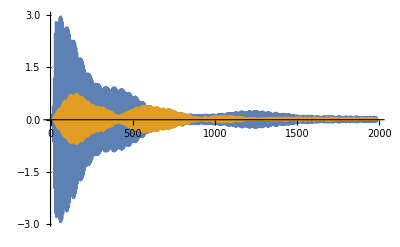

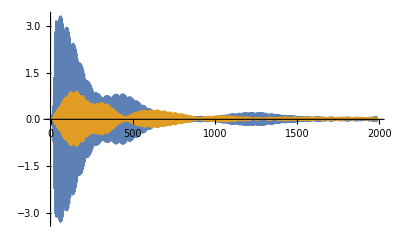

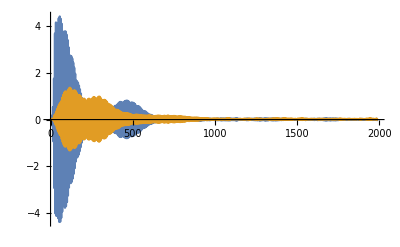

```mathematica
"DELTA = 0.02; Series: Zx = 1, 2, 2.2"
data=Import["F:/iyaf/Zx=1,delt=0,02coord.dat"];
ListPlot[(data[[Range[25,5000],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->{-5,5}]
data=Import["F:/iyaf/Zx=2,delt=0,02coord.dat"];
ListPlot[(data[[Range[25,5000],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->{-5,5}]
data=Import["F:/iyaf/Zx=2,3,delt=0,02coord.dat"];
ListPlot[Re[InverseFourier[Table[{(n-1)/(nf-ni+1)/.{ni->2,nf->2000},(((0.001/(0.001+(((n-1)/(nf-ni+1))-0.17)^2))+(0.001/(0.001+(((n-1)/(nf-ni+1))-(1-0.17))^2)))/.{ni->2,nf->2000})Fourier[data[[Range[ni/.{ni->2,nf->2000},nf/.{ni->2,nf->2000}],#]]][[n]]},{n,(nf-ni+1)/.{ni->2,nf->2000}}][[All,2]]]][[Range[10,1999]]]&/@{2,3},PlotRange->All,Joined->True,PlotMarkers->None]
"DELTA = 0; Series: Zx = "
data=Import["F:/iyaf/Zx=0,12,delt=0coord.dat"];
ListPlot[(data[[Range[25,5000],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->{-5,5}]
data=Import["F:/iyaf/Zx=0,73,delt=0coord.dat"];
ListPlot[(data[[Range[25,5000],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->{-5,5}]
data0=Import["F:/iyaf/Zx=1,42,delt=0coord.dat"];
ListPlot[(data0[[Range[25,5000],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->{-5,5}]
data=Import["F:/iyaf/Zx=2,2,delt=0coord.dat"];
ListPlot[Re[InverseFourier[Table[{(n-1)/(nf-ni+1)/.{ni->2,nf->2000},(((0.001/(0.001+(((n-1)/(nf-ni+1))-0.17)^2))+(0.001/(0.001+(((n-1)/(nf-ni+1))-(1-0.17))^2)))/.{ni->2,nf->2000})Fourier[data[[Range[ni/.{ni->2,nf->2000},nf/.{ni->2,nf->2000}],#]]][[n]]},{n,(nf-ni+1)/.{ni->2,nf->2000}}][[All,2]]]][[Range[10,1999]]]&/@{2,3},PlotRange->All,Joined->True,PlotMarkers->None,AxesLabel->{"n","x,y"},LabelStyle->Directive[Black, 14]]
data=Import["F:/iyaf/Zx=2,7,delt=0coord.dat"];
ListPlot[Re[InverseFourier[Table[{(n-1)/(nf-ni+1)/.{ni->2,nf->2000},(((0.001/(0.001+(((n-1)/(nf-ni+1))-0.17)^2))+(0.001/(0.001+(((n-1)/(nf-ni+1))-(1-0.17))^2)))/.{ni->2,nf->2000})Fourier[data[[Range[ni/.{ni->2,nf->2000},nf/.{ni->2,nf->2000}],#]]][[n]]},{n,(nf-ni+1)/.{ni->2,nf->2000}}][[All,2]]]][[Range[10,1999]]]&/@{2,3},PlotRange->All,Joined->True,PlotMarkers->None]
data=Import["F:/iyaf/Zx=3,15,delt=0coord.dat"];
ListPlot[Re[InverseFourier[Table[{(n-1)/(nf-ni+1)/.{ni->2,nf->2000},(((0.001/(0.001+(((n-1)/(nf-ni+1))-0.17)^2))+(0.001/(0.001+(((n-1)/(nf-ni+1))-(1-0.17))^2)))/.{ni->2,nf->2000})Fourier[data[[Range[ni/.{ni->2,nf->2000},nf/.{ni->2,nf->2000}],#]]][[n]]},{n,(nf-ni+1)/.{ni->2,nf->2000}}][[All,2]]]][[Range[10,1999]]]&/@{2,3},PlotRange->All,Joined->True,PlotMarkers->None]
data=Import["F:/iyaf/Zx=3,5,delt=0coord.dat"];
ListPlot[Re[InverseFourier[Table[{(n-1)/(nf-ni+1)/.{ni->2,nf->2000},(((0.001/(0.001+(((n-1)/(nf-ni+1))-0.17)^2))+(0.001/(0.001+(((n-1)/(nf-ni+1))-(1-0.17))^2)))/.{ni->2,nf->2000})Fourier[data[[Range[ni/.{ni->2,nf->2000},nf/.{ni->2,nf->2000}],#]]][[n]]},{n,(nf-ni+1)/.{ni->2,nf->2000}}][[All,2]]]][[Range[10,1999]]]&/@{2,3},PlotRange->All,Joined->True,PlotMarkers->None]
data0=Import["F:/iyaf/Zx=4,4,delt=0coord.dat"];
ListPlot[Re[InverseFourier[Table[{(n-1)/(nf-ni+1)/.{ni->2,nf->2000},(((0.001/(0.001+(((n-1)/(nf-ni+1))-0.17)^2))+(0.001/(0.001+(((n-1)/(nf-ni+1))-(1-0.17))^2)))/.{ni->2,nf->2000})Fourier[data0[[Range[ni/.{ni->2,nf->2000},nf/.{ni->2,nf->2000}],#]]][[n]]},{n,(nf-ni+1)/.{ni->2,nf->2000}}][[All,2]]]][[Range[10,1999]]]&/@{2,3},PlotRange->All,Joined->True,PlotMarkers->None]
data=Import["F:/iyaf/Zx=5,9,delt=0coord.dat"];
ListPlot[Re[InverseFourier[Table[{(n-1)/(nf-ni+1)/.{ni->2,nf->2000},(((0.001/(0.001+(((n-1)/(nf-ni+1))-0.17)^2))+(0.001/(0.001+(((n-1)/(nf-ni+1))-(1-0.17))^2)))/.{ni->2,nf->2000})Fourier[data[[Range[ni/.{ni->2,nf->2000},nf/.{ni->2,nf->2000}],#]]][[n]]},{n,(nf-ni+1)/.{ni->2,nf->2000}}][[All,2]]]][[Range[10,1999]]]&/@{2,3},PlotRange->All,Joined->True,PlotMarkers->None]
```

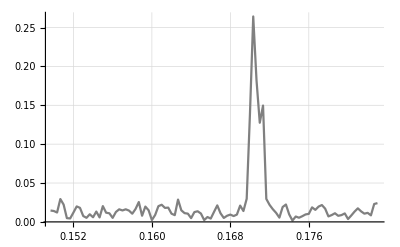

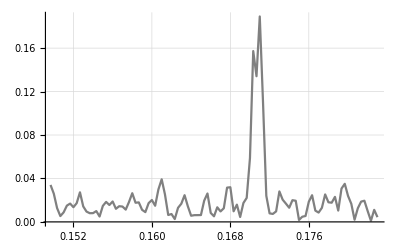

```mathematica
data0=Import["F:/iyaf/Zx=0,12,delt=0coord.dat"];
xwind=Table[(Sin[(i-1) π/3000])^2 data0[[i,2]],{i,2,3001}];
ywind=Table[(Sin[(i-1)π/3000])^2 data0[[i,3]],{i,2,3001}];
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[xwind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[ywind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

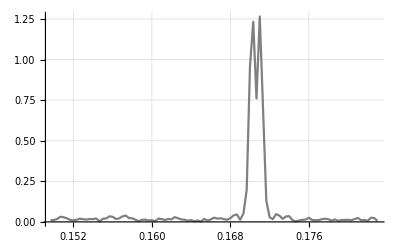

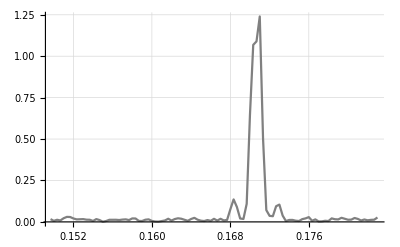

```mathematica
data0=Import["F:/iyaf/Zx=0,73,delt=0coord.dat"];
xwind=Table[(Sin[(i-1) π/3000])^2 data0[[i,2]],{i,2,3001}];
ywind=Table[(Sin[(i-1)π/3000])^2 data0[[i,3]],{i,2,3001}];
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[xwind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[ywind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

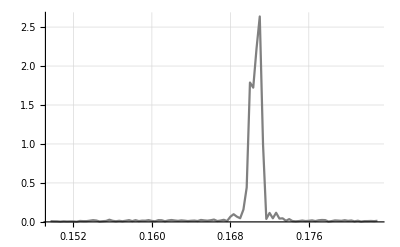

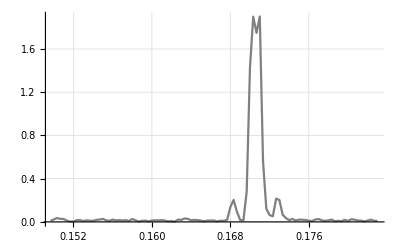

```mathematica
data0=Import["F:/iyaf/Zx=1,42,delt=0coord.dat"];
xwind=Table[(Sin[(i-1) π/3000])^2 data0[[i,2]],{i,2,3001}];
ywind=Table[(Sin[(i-1)π/3000])^2 data0[[i,3]],{i,2,3001}];
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[xwind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[ywind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

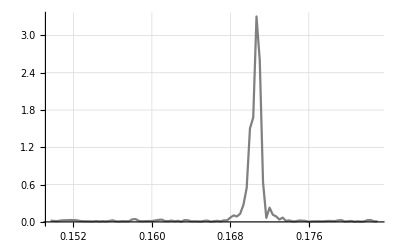

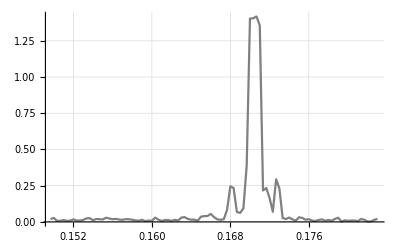

```mathematica
data0=Import["F:/iyaf/Zx=2,2,delt=0coord.dat"];
xwind=Table[(Sin[(i-1) π/3000])^2 data0[[i,2]],{i,2,3001}];
ywind=Table[(Sin[(i-1)π/3000])^2 data0[[i,3]],{i,2,3001}];
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[xwind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[ywind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

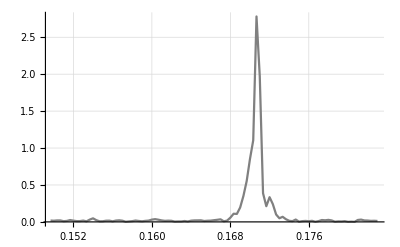

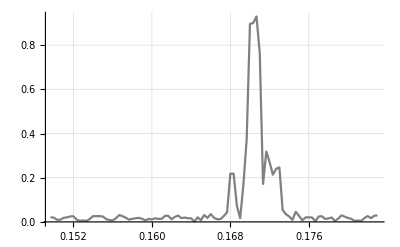

```mathematica
data0=Import["F:/iyaf/Zx=2,7,delt=0coord.dat"];
xwind=Table[(Sin[(i-1) π/3000])^2 data0[[i,2]],{i,2,3001}];
ywind=Table[(Sin[(i-1)π/3000])^2 data0[[i,3]],{i,2,3001}];
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[xwind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[ywind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

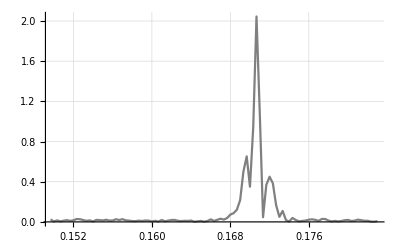

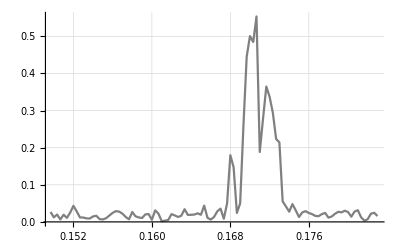

```mathematica
data0=Import["F:/iyaf/Zx=3,15,delt=0coord.dat"];
xwind=Table[(Sin[(i-1) π/3000])^2 data0[[i,2]],{i,2,3001}];
ywind=Table[(Sin[(i-1)π/3000])^2 data0[[i,3]],{i,2,3001}];
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[xwind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[ywind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

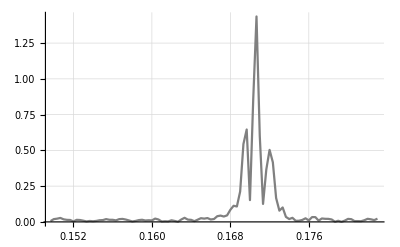

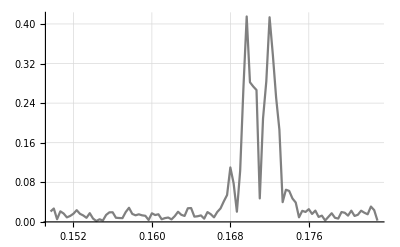

```mathematica
data0=Import["F:/iyaf/Zx=3,5,delt=0coord.dat"];
xwind=Table[(Sin[(i-1) π/3000])^2 data0[[i,2]],{i,2,3001}];
ywind=Table[(Sin[(i-1)π/3000])^2 data0[[i,3]],{i,2,3001}];
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[xwind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[ywind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

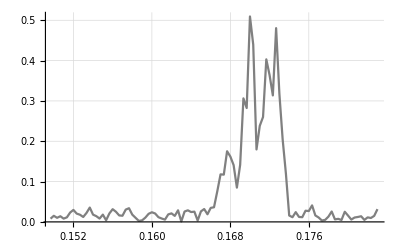

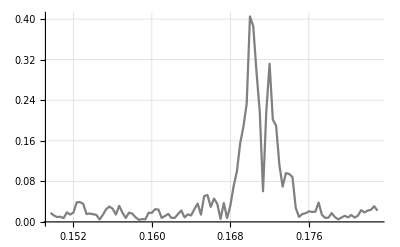

```mathematica
data0=Import["F:/iyaf/Zx=4,4,delt=0coord.dat"];
xwind=Table[(Sin[(i-1) π/3000])^2 data0[[i,2]],{i,2,3001}];
ywind=Table[(Sin[(i-1)π/3000])^2 data0[[i,3]],{i,2,3001}];
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[xwind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[ywind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

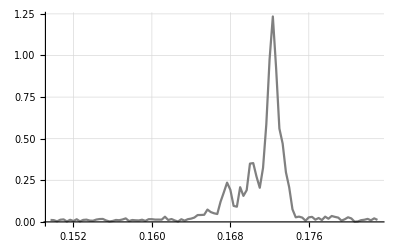

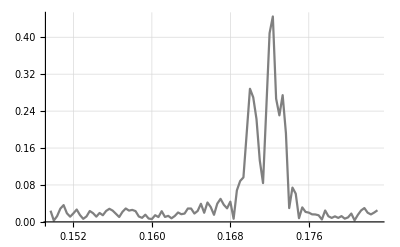

```mathematica
data0=Import["F:/iyaf/Zx=5,9,delt=0coord.dat"];
xwind=Table[(Sin[(i-1) π/3000])^2 data0[[i,2]],{i,2,3001}];
ywind=Table[(Sin[(i-1)π/3000])^2 data0[[i,3]],{i,2,3001}];
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[xwind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(3000),Abs[Fourier[ywind]][[n1]]},{n1,1,3000}][[Range[450,550]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

DELTA = 0.02; Series: Zx = 1, 2, 2.2

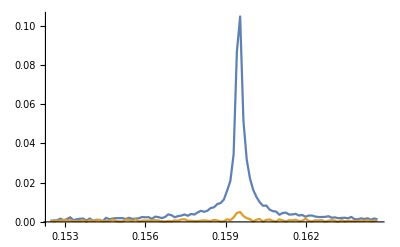

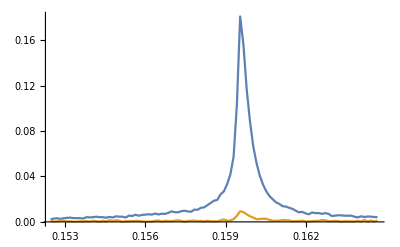

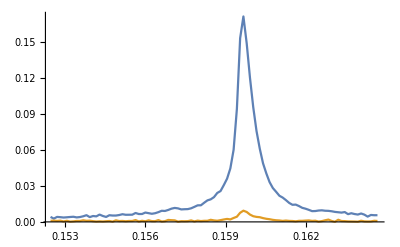

DELTA = 0; Series: Zx =

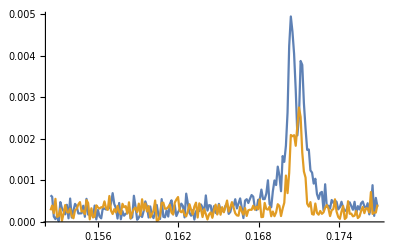

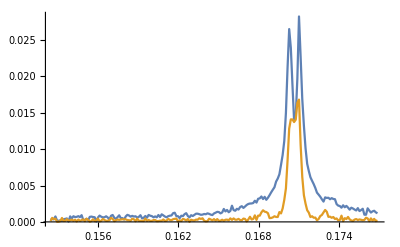

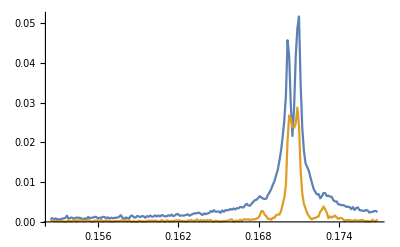

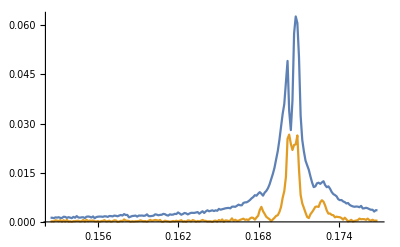

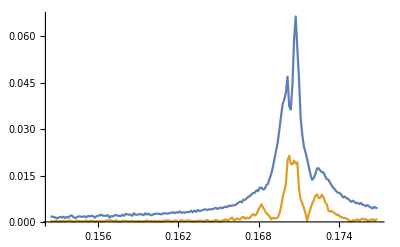

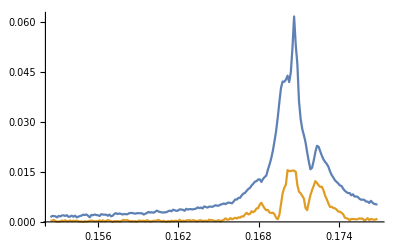

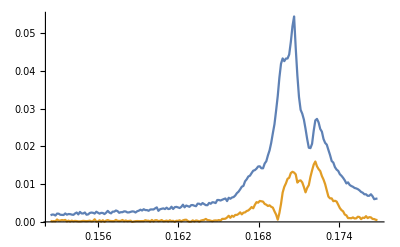

-Graphics-

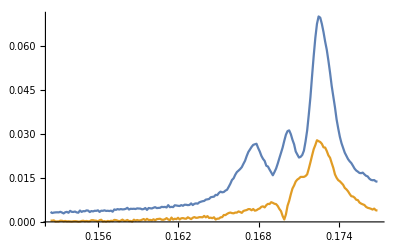

```mathematica
"DELTA = 0.02; Series: Zx = 1, 2, 2.2"
data=Import["F:/iyaf/Zx=1,delt=0,02spect.dat"];
ListPlot[(data[[Range[1250,1350],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data=Import["F:/iyaf/Zx=2,delt=0,02spect.dat"];
ListPlot[(data[[Range[1250,1350],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data=Import["F:/iyaf/Zx=2,3,delt=0,02spect.dat"];
ListPlot[(data[[Range[1250,1350],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
"DELTA = 0; Series: Zx = "
data=Import["F:/iyaf/Zx=0,12,delt=0spect.dat"];
ListPlot[(data[[Range[1250,1450],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data=Import["F:/iyaf/Zx=0,73,delt=0spect.dat"];
ListPlot[(data[[Range[1250,1450],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data0=Import["F:/iyaf/Zx=1,42,delt=0spect.dat"];
ListPlot[(data0[[Range[1250,1450],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data=Import["F:/iyaf/Zx=2,2,delt=0spect.dat"];
ListPlot[(data[[Range[1250,1450],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data=Import["F:/iyaf/Zx=2,7,delt=0spect.dat"];
ListPlot[(data[[Range[1250,1450],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data=Import["F:/iyaf/Zx=3,15,delt=0spect.dat"];
ListPlot[(data[[Range[1250,1450],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data=Import["F:/iyaf/Zx=3,5,delt=0spect.dat"];
ListPlot[(data[[Range[1250,1450],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data0=Import["F:/iyaf/Zx=4,4,delt=0spect.dat"];
ListPlot[(data[[Range[1250,1450],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
data=Import["F:/iyaf/Zx=5,9,delt=0spect.dat"];
ListPlot[(data[[Range[1250,1450],{1,#}]]&/@{2,3}),Joined->True,PlotMarkers->None,PlotRange->All]
```

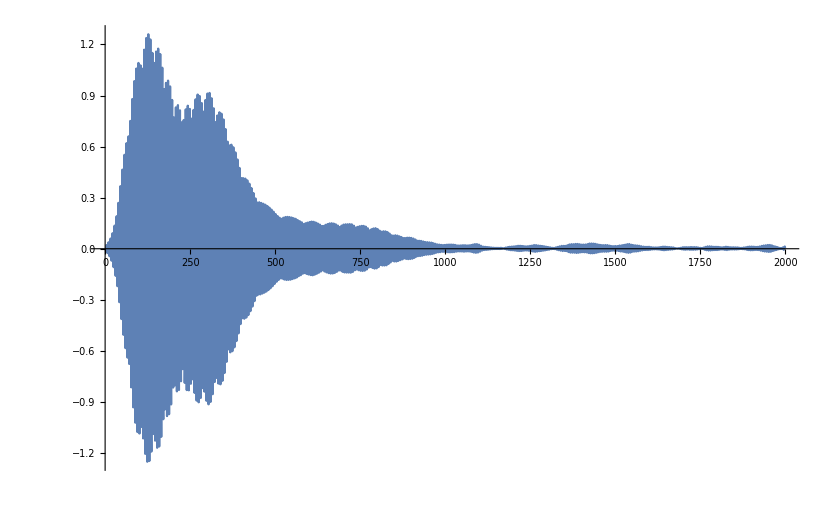

```mathematica
ListPlot[Re[InverseFourier[Table[{(n-1)/(nf-ni+1)/.{ni->2,nf->2000},(((0.0001/(0.0001+(((n-1)/(nf-ni+1))-0.17)^2))+(0.0001/(0.0001+(((n-1)/(nf-ni+1))-(1-0.17))^2)))/.{ni->2,nf->2000})Fourier[data0[[Range[ni/.{ni->2,nf->2000},nf/.{ni->2,nf->2000}],3]]][[n]]},{n,(nf-ni+1)/.{ni->2,nf->2000}}][[All,2]]]][[Range[1,1999]]],PlotRange->All,Joined->True,PlotMarkers->None]
```

```mathematica
Fxx=Exp[-xx^2Zx^2/(2 .01.01(1+xx^2))]/(1+xx^2);
Fzz=Exp[-zz^2Zz^2/(2 .01.01(1+zz^2))]/(1+zz^2);
Fxz=Exp[-xz^2Zz^2/(2 .01.01(1+xz^2))]/(1+xz^2);
Fzx=Exp[-zx^2Zx^2/(2 .01.01(1+zx^2))]/(1+zx^2);
xx=4 π .01.01kxx n;
zz=4 π.01.01 kzz n;
xz=4 π.01.01 kxz n;
zx=4 π.01.01 kzx n;
```

```mathematica
a1=wx Cos[γ]Exp[I ((νx+νy+2+η)/2) 2 π n];
a1c=wx Cos[γ]Exp[-I ((νx+νy+2+η)/2) 2 π n];
a3=wy Sin[γ] Exp[I ((νx+νy-2+η)/2) 2 π n-I α];
a3c=wy Sin[γ] Exp[-I ((νx+νy-2+η)/2) 2 π n+I α];
b1=-Sin[γ]wx Exp[I ((νx+νy+2-η)/2) 2 π n];
b1c=-Sin[γ]wx Exp[-I ((νx+νy+2-η)/2) 2 π n];
b3=wy Cos[γ] Exp[I ((νx+νy-2-η)/2) 2 π n-I α];
b3c=wy Cos[γ] Exp[-I ((νx+νy-2-η)/2) 2 π n+I α];
```

```mathematica
x=A1 (a1 +a1c )+B1(b1+b1c);(*без расфазировки*)
y=A1(a3 +a3c )+B1(b3 +b3c);(*без расфазировки*)
```

```mathematica
Δϕa=2 ArcTan[xx]+2ArcTan[xz]+xx Zx^2/(2 .01.01(1+xx^2))+xz Zz^2/(2 .01.01(1+xz^2));
Δϕb=2 ArcTan[zz]+2ArcTan[zx]+zz Zz^2/(2 .01.01 (1+zz^2))+zx Zx^2/(2 .01.01(1+zx^2));
```

```mathematica
x=A1 (a1 Exp[I Δϕa] +a1c Exp[-I Δϕa])+Exp[I π]B1(b1 Exp[I Δϕb]+b1c Exp[-I Δϕb])/.{Zx->0.1,Zz->0.1,kxx->8,kxz->8,kzz->8,kzx->8};
y=Exp[-I π]A1(a3 Exp[I Δϕa] +a3c Exp[-I Δϕa])+B1(b3 Exp[I Δϕb]+b3c Exp[-I Δϕb])/.{Zx->0.1,Zz->0.1,kxx->8,kxz->8,kzz->8,kzx->8};
```

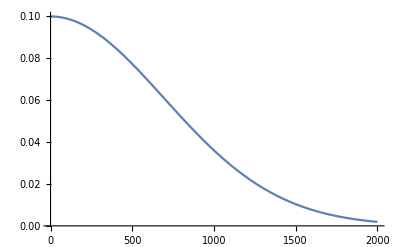

```mathematica
AA=(Zx Fxx Fxz )/.{Zx->.1,Zz->0.1,νa->0,kxx->8,kxz->8};
BB=(Zz Fzz Fzx )/.{Zx->.1,Zz->0.1,νb->0,kzz->8,kzx->8};
Plot[AA,{n,0,2000},PlotRange->All]
```

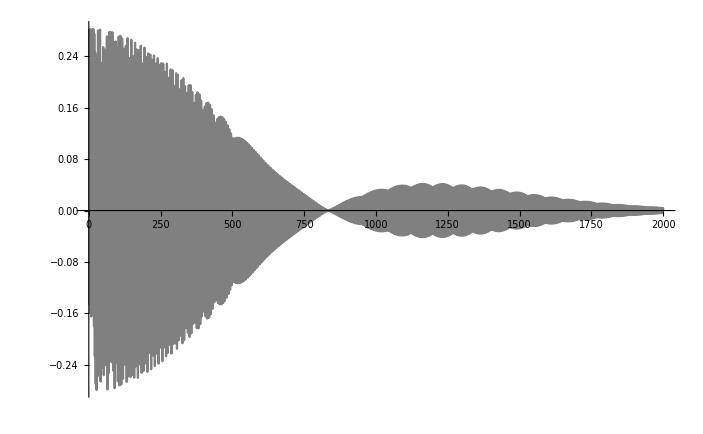

```mathematica
plotx=ListPlot[Table[(x/.{γ->π/4,η->0.0006,wx->1,wy->1,A1->AA,B1->BB,νx->4.17,νy->2.17}),{n,0,2000}],PlotStyle->Gray,PlotRange->All,Joined->True]
```

```mathematica
listfourierx=Abs[Fourier[Table[x/.{γ->π/4,η->0.0006,wx->1,wy->1,A1->AA,B1->BB,νx->4.17,νy->2.17,νa->0,νb->0},{n,0,10000}]]];
listfouriery=Abs[Fourier[Table[y/.{γ->π/4,η->0.0006,wx->1,wy->1,A1->AA,B1->BB,νx->4.17,νy->2.17,νa->0,νb->0,α->π/2},{n,0,10000}]]];
```

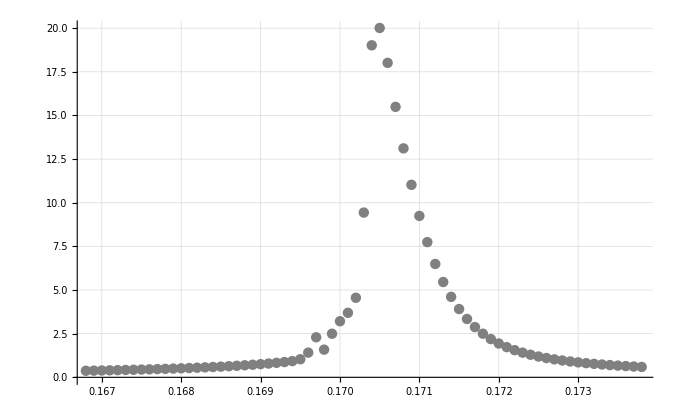

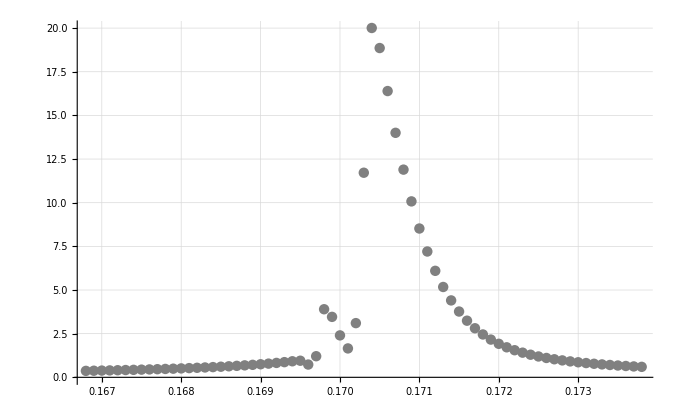

```mathematica
ListPlot[Table[{(n1-1)/(10000),listfourierx[[n1]]},{n1,0,10000}][[Range[1670,1740]]],PlotStyle->Gray,PlotRange->All,Joined->False,GridLines->Automatic]
ListPlot[Table[{(n1-1)/(10000),listfouriery[[n1]]},{n1,0,10000}][[Range[1670,1740]]],PlotStyle->Gray,PlotRange->All,Joined->False,GridLines->Automatic]
```

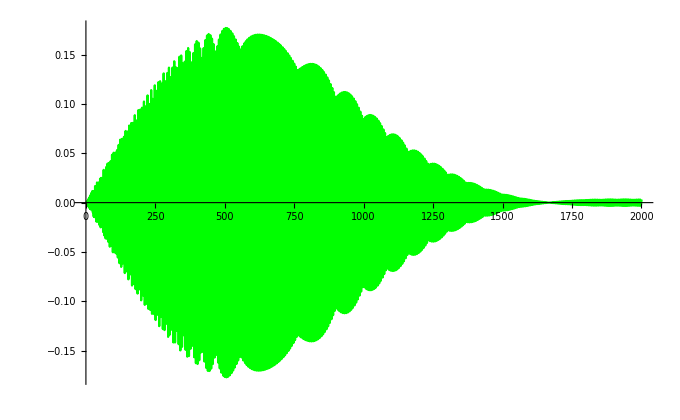

```mathematica
ploty=ListPlot[Table[(y/.{γ->π/4,η->0.0006,wx->1,wy->1,A1->AA,B1->BB,νx->4.17,νy->2.17,α->0}),{n,0,2000}],PlotStyle->Green,PlotRange->All,Joined->True]
```

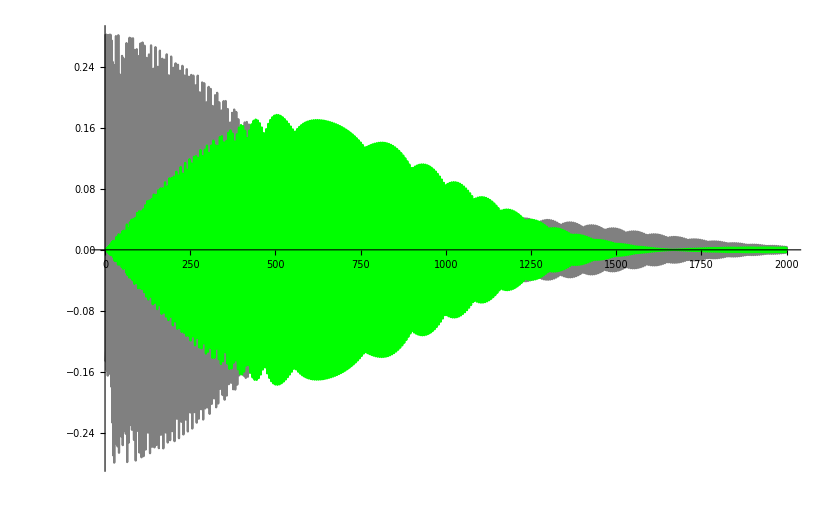

```mathematica
Show[{plotx,ploty},PlotRange->All]
```

```mathematica
h:=1/2(k11 Jx^3/2 Sqrt[Jy]+k12 Sqrt[Jx] Jy^3/2)(Cos[ϕx-ϕy+η n 2π])+3/8(p Jx^2+r Jy^2+2 q Jx Jy)-3/4f2 Jx Jy (Cos[2ϕx-2ϕy+2η n 2π])+k1 Cos[ϕx+2 π s(νx+νy+η)/2-wr s]Sqrt[Jx]+k2 Cos[ϕy+2 π s(νx+νy-η)/2-wr s]Sqrt[Jy]
ϕxstr=D[h,Jx];
Jxstr=-D[h,ϕx];
ϕystr=D[h,Jy];
Jystr=-D[h,ϕy];
Jxstrd=Jxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
Jystrd=Jystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕxstrd=ϕxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕystrd=ϕystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
```

```mathematica
inputpr=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{f2->f2,k11->k11,k12->k12,p->p,r->r,q->q,η->η,n->t,k1->k1,k2->k2,νx->νx,νy->νy,wr->wr,s->t});
```

```mathematica
inloc=inputpr/.{Jxv->a^2,Jyv->b^2,ϕxv->ϕa,ϕyv->ϕb,f2->0,k11->0,k12->0,p->.5,r->.5,q->-.5,η->0.001,k1->0,k2->0,νx->0,νy->0,wr->0};
tablesol=Table[Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,5000}]],{a,.08,.12,.01},{b,.08,.12,.01},{ϕa,0,2π-0.01,2π/10},{ϕb,0,2π-0.01,2π/10}];
```

```mathematica
podsum=Table[(10((a b)/(2 π σx σy)^2(Sqrt[Jx[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}]Exp[-(a^2+Z1^2)/(2σx^2)]Exp[-(b^2+Z2^2)/(2σy^2)]Exp[(Z1 a Sin[ϕa])/σx^2]Exp[(Z2 b Sin[ϕb])/σy^2])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νx0->0.1705,n->t1,a->0.08+0.01(i-1),b->0.08+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10})0.01 0.01 (2π/10 )(2π/10),{i,1,5},{j,1,5},{k,1,10},{l,1,10}];
```

```mathematica
tablea=Table[{t1,Total[Flatten[podsum]]},{t1,0,3000,1}];
```

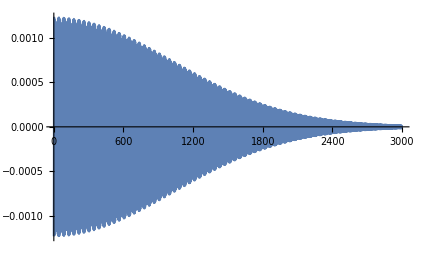

```mathematica
ListPlot[tablea,Joined->True,PlotRange->All]
```

```mathematica
podsumb=Table[(10((a b)/(2 π σx σy)^2(Sqrt[Jy[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}]Exp[-(a^2+Z1^2)/(2σx^2)]Exp[-(b^2+Z2^2)/(2σy^2)]Exp[(Z1 a Sin[ϕa])/σx^2]Exp[(Z2 b Sin[ϕb])/σy^2])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νy0->0.1695,n->t1,a->0.08+0.01(i-1),b->0.08+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10})0.01 0.01(2π/10 )(2π/10),{i,1,5},{j,1,5},{k,1,10},{l,1,10}];
```

```mathematica
tableb=Table[{t1,Total[Flatten[podsumb]]},{t1,0,3000,1}];
```

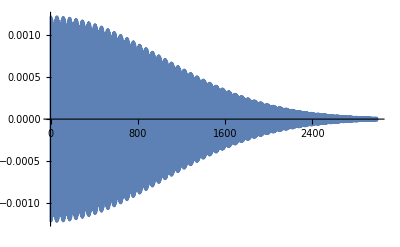

```mathematica
ListPlot[tableb,Joined->True,PlotRange->All]
```

```mathematica
a1=wx Cos[γ];
a1c=wx Cos[γ];
a3=wy Sin[γ] ;
a3c=wy Sin[γ];
b1=-Sin[γ]wx ;
b1c=-Sin[γ]wx ;
b3=wy Cos[γ];
b3c=wy Cos[γ] ;
```

```mathematica
x=a1 tablea[[All,2]]-b1 tableb[[All,2]];
y=-a3 tablea[[All,2]]+b3 tableb[[All,2]];
```

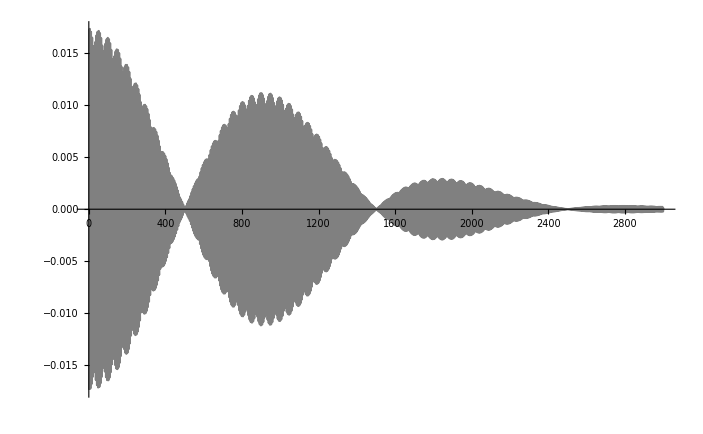

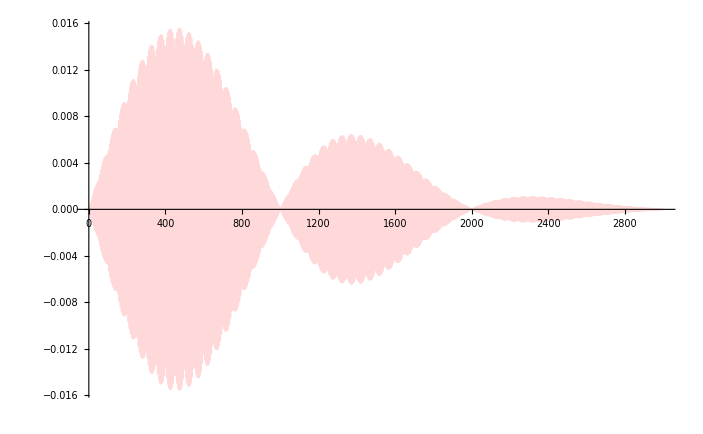

```mathematica
plotx=ListPlot[x[[Range[0,3000]]]/.{wx->10,γ->π/4,wy->10},PlotStyle->Gray,PlotRange->All,Joined->True]
ploty=ListPlot[y/.{wx->10,γ->π/4,wy->10,α->0},PlotStyle->LightRed,PlotRange->All,Joined->True]
```

```mathematica
listfourierx=Abs[Fourier[x/.{wx->10,γ->π/4,wy->10}]];
listfouriery=Abs[Fourier[y/.{wx->10,γ->π/4,wy->10,α->0}]];
```

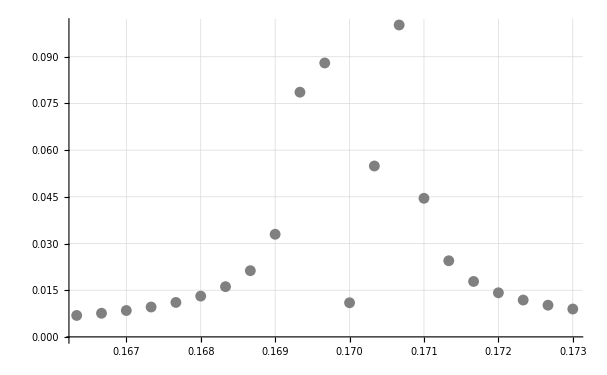

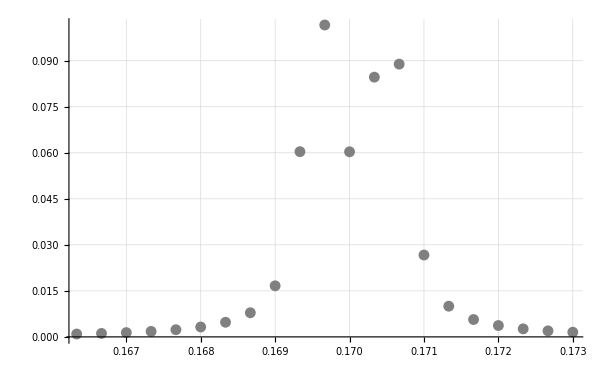

```mathematica
ListPlot[Table[{(n1-1)/(3000),listfourierx[[n1]]},{n1,1,3000}][[Range[500,520]]],PlotStyle->Gray,PlotRange->All,Joined->False,GridLines->Automatic]
ListPlot[Table[{(n1-1)/(3000),listfouriery[[n1]]},{n1,1,3000}][[Range[500,520]]],PlotStyle->Gray,PlotRange->All,Joined->False,GridLines->Automatic]
```

```mathematica
inloc=inputpr/.{Jxv->a^2,Jyv->b^2,ϕxv->ϕa,ϕyv->ϕb,f2->.5,k11->0,k12->0,p->.5,r->.5,q->-.5,η->0.001,k1->0,k2->0};
tablesol=Table[Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,1000}]],{a,.08,.12,.01},{b,.08,.12,.01},{ϕa,0,2π-0.01,2π/10},{ϕb,0,2π-0.01,2π/10}];
```

```mathematica
podsum=Table[(10((a b)/(2 π σx σy)^2(Sqrt[Jx[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}]Exp[-(a^2+Z1^2)/(2σx^2)]Exp[-(b^2+Z2^2)/(2σy^2)]Exp[(Z1 a Sin[ϕa])/σx^2]Exp[(Z2 b Sin[ϕb])/σy^2])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νx0->0.1705,n->t1,a->0.08+0.01(i-1),b->0.08+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10})0.01 0.01 (2π/10 )(2π/10),{i,1,5},{j,1,5},{k,1,10},{l,1,10}];
```

```mathematica
tablea=Table[{t1,Total[Flatten[podsum]]},{t1,0,1000,1}];
```

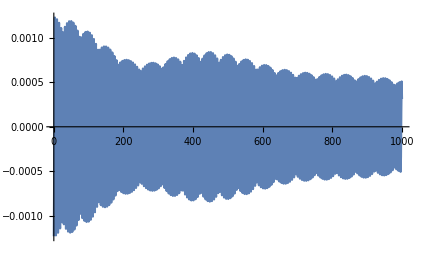

```mathematica
ListPlot[tablea,Joined->True,PlotRange->All]
```

```mathematica
podsumb=Table[(10((a b)/(2 π σx σy)^2(Sqrt[Jy[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}]Exp[-(a^2+Z1^2)/(2σx^2)]Exp[-(b^2+Z2^2)/(2σy^2)]Exp[(Z1 a Sin[ϕa])/σx^2]Exp[(Z2 b Sin[ϕb])/σy^2])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νy0->0.1695,n->t1,a->0.08+0.01(i-1),b->0.08+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10})0.01 0.01(2π/10 )(2π/10),{i,1,5},{j,1,5},{k,1,10},{l,1,10}];
```

```mathematica
tableb=Table[{t1,Total[Flatten[podsumb]]},{t1,0,1000,1}];
```

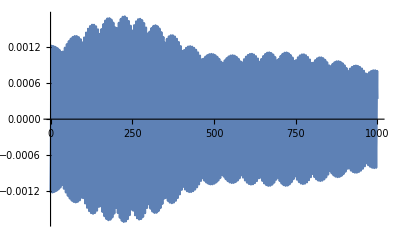

```mathematica
ListPlot[tableb,Joined->True,PlotRange->All]
```

```mathematica
a1=wx Cos[γ];
a1c=wx Cos[γ];
a3=wy Sin[γ] Cos[α];
a3c=wy Sin[γ];
b1=-Sin[γ]wx Cos[α];
b1c=-Sin[γ]wx ;
b3=wy Cos[γ];
b3c=wy Cos[γ] ;
```

```mathematica
x=a1 tablea[[All,2]]+b1 tableb[[All,2]];
y=a3 tablea[[All,2]]+b3 tableb[[All,2]];
```

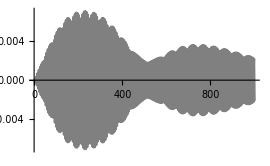

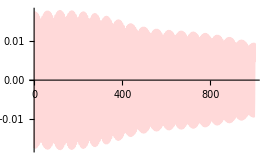

```mathematica
plotx=ListPlot[x[[Range[0,1000]]]/.{wx->10,γ->π/4,wy->10,α->0},PlotStyle->Gray,PlotRange->All,Joined->True]
ploty=ListPlot[y/.{wx->10,γ->π/4,wy->10,α->0},PlotStyle->LightRed,PlotRange->All,Joined->True]
```

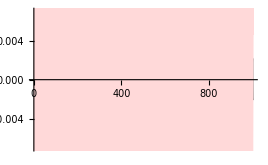

```mathematica
Show[{plotx,ploty}]
```

```mathematica
listfourierx=Abs[Fourier[x/.{wx->10,γ->π/4,wy->10,α->0}]];
listfouriery=Abs[Fourier[y/.{wx->10,γ->π/4,wy->10,α->0}]];
```

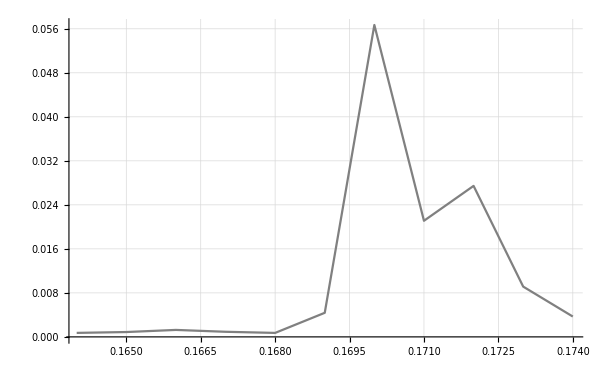

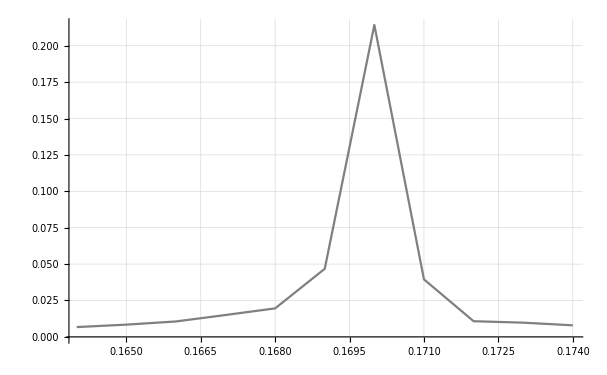

```mathematica
ListPlot[Table[{(n1-1)/(1000),listfourierx[[n1]]},{n1,1,1001}][[Range[165,175]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
ListPlot[Table[{(n1-1)/(1000),listfouriery[[n1]]},{n1,1,1001}][[Range[165,175]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

```mathematica
inloc=inputpr/.{Jxv->a^2/100,Jyv->b^2/100,ϕxv->ϕa,ϕyv->ϕb,f2->50,k11->0,k12->0,p->30,r->30,q->-30,η->0.001,k1->.0001,k2->.0001,νx->.17,νy->.17,wr->.1715,n->t};
tablesol=Table[Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,1000}]],{a,.08,.12,.01},{b,.08,.12,.01},{ϕa,0,2π-0.01,2π/10},{ϕb,0,2π-0.01,2π/10}];
```

```mathematica
podsum=Table[(10((a b)/(2 π σx σy)^2(Sqrt[Jx[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}]Exp[-(a^2+Z1^2)/(2σx^2)]Exp[-(b^2+Z2^2)/(2σy^2)]Exp[(Z1 a Sin[ϕa])/σx^2]Exp[(Z2 b Sin[ϕb])/σy^2])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νx0->0.1705,n->t1,a->0.08+0.01(i-1),b->0.08+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10})0.01 0.01 (2π/10 )(2π/10),{i,1,5},{j,1,5},{k,1,10},{l,1,10}];
```

```mathematica
tablea=Table[{t1,Total[Flatten[podsum]]},{t1,0,1000,1}];
```

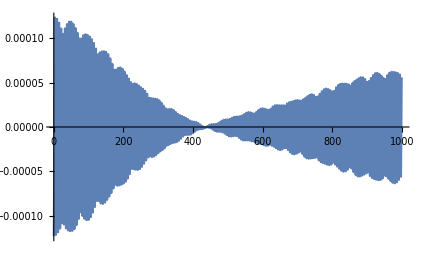

```mathematica
ListPlot[tablea,Joined->True,PlotRange->All]
```

```mathematica
podsumb=Table[(10((a b)/(2 π σx σy)^2(Sqrt[Jy[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}]Exp[-(a^2+Z1^2)/(2σx^2)]Exp[-(b^2+Z2^2)/(2σy^2)]Exp[(Z1 a Sin[ϕa])/σx^2]Exp[(Z2 b Sin[ϕb])/σy^2])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νy0->0.1695,n->t1,a->0.08+0.01(i-1),b->0.08+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10})0.01 0.01(2π/10 )(2π/10),{i,1,5},{j,1,5},{k,1,10},{l,1,10}];
```

```mathematica
tableb=Table[{t1,Total[Flatten[podsumb]]},{t1,0,1000,1}];
```

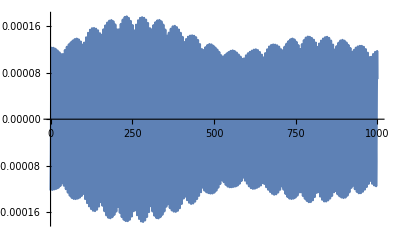

```mathematica
ListPlot[tableb,Joined->True,PlotRange->All]
```

```mathematica
a1=wx Cos[γ];
a1c=wx Cos[γ];
a3=wy Sin[γ] ;
a3c=wy Sin[γ];
b1=-Sin[γ]wx ;
b1c=-Sin[γ]wx ;
b3=wy Cos[γ];
b3c=wy Cos[γ] ;
```

```mathematica
x=a1 tablea[[All,2]]+b1 tableb[[All,2]];
y=a3 tablea[[All,2]]+b3 tableb[[All,2]];
```

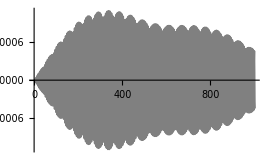

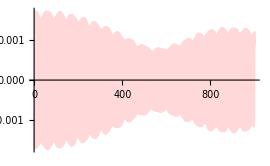

```mathematica
plotx=ListPlot[x[[Range[0,1000]]]/.{wx->10,γ->π/4,wy->10},PlotStyle->Gray,PlotRange->All,Joined->True]
ploty=ListPlot[y/.{wx->10,γ->π/4,wy->10,α->0},PlotStyle->LightRed,PlotRange->All,Joined->True]
```

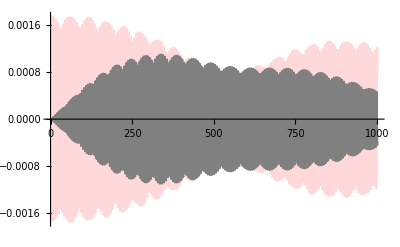

```mathematica
Show[{ploty,plotx}]
```

```mathematica
xwind=Table[(Sin[i π/1000])^2 x[[i]],{i,0,1000}];
ywind=Table[(Sin[i π/1000])^2 y[[i]],{i,0,1000}];
```

```mathematica
listfourierx=Abs[Fourier[xwind/.{wx->10,γ->π/4,wy->10}]];
listfouriery=Abs[Fourier[ywind/.{wx->10,γ->π/4,wy->10,α->0}]];
```

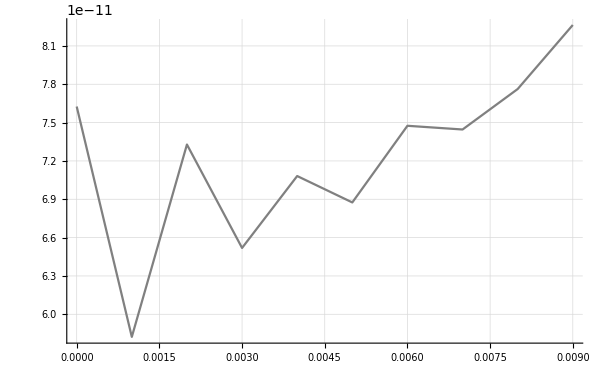

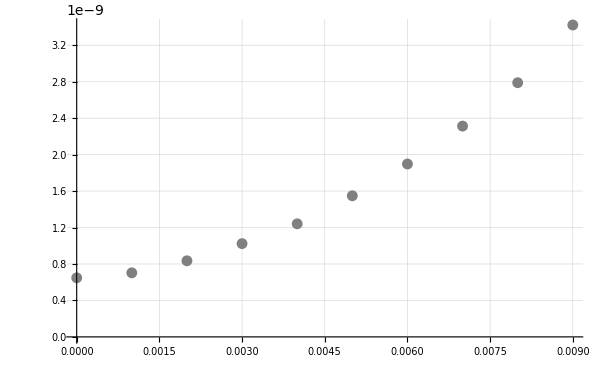

```mathematica
ListPlot[Table[{(n1-1)/(1000),listfourierx[[n1]]},{n1,1,1001}][[Range[0,10]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
ListPlot[Table[{(n1-1)/(1000),listfouriery[[n1]]},{n1,1,1001}][[Range[0,10]]],PlotStyle->Gray,PlotRange->All,Joined->False,GridLines->Automatic]
```

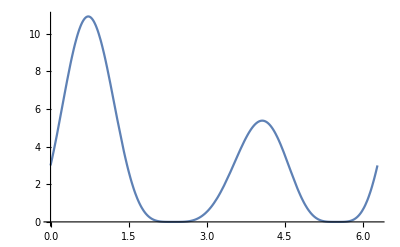

```mathematica
Plot[(2+Cos[x])(1+Sin[2x])^2,{x,0,2π}]
```